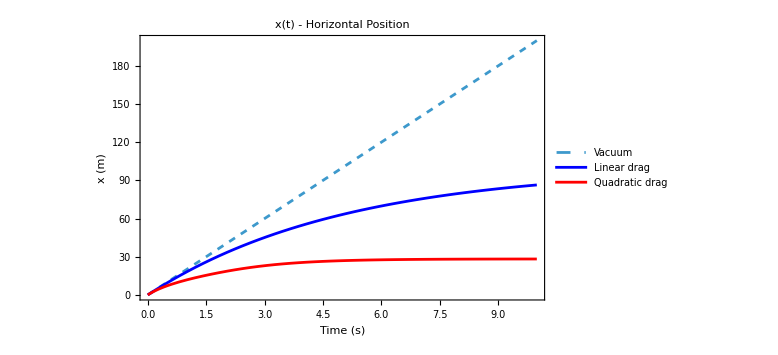
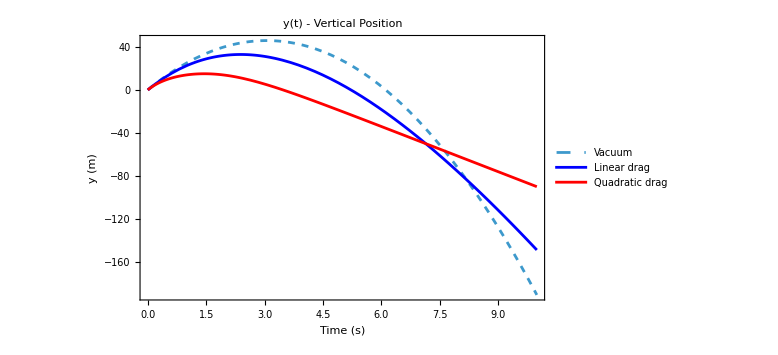
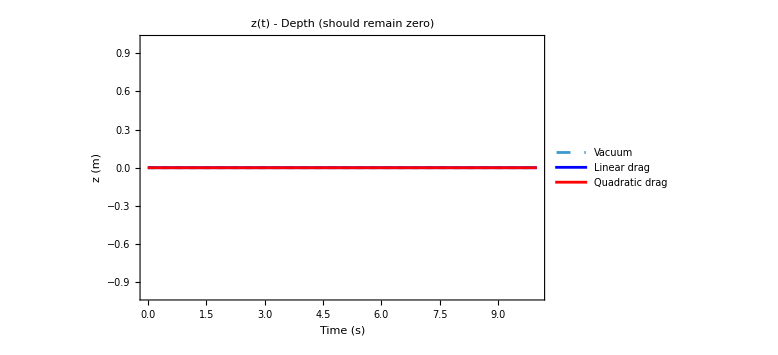

-Graphics3D-

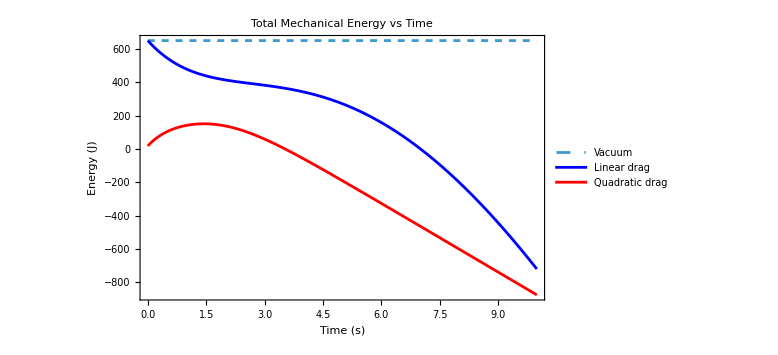

```mathematica
(*This Wolfram Language (Mathematica) notebook is based on Classical Mechanics of the Physics course at UNESP Bauru.
It compares the position (x,y,z) of a particle moving under gravity in:
   1. Vacuum (no air resistance)
 2. Gradual atmosphere (linear drag,F_drag=-k*v)
 3. Earth-like atmosphere (quadratic drag,F_drag=-c*v^2)*)ClearAll["Global`*"];

(* =======================================*)
(*PHYSICAL PARAMETERS*)
(* =======================================*)
m=1;              (*Mass of the particle[kg]*)
g=9.81;           (*Gravity[m/s^2]*)
v0x=20;           (*Initial horizontal velocity[m/s]*)
v0y=30;           (*Initial vertical velocity[m/s]*)
v0z=0;            (*No initial vertical motion in z*)
k=0.2;            (*Linear drag coefficient[kg/s]*)
c=0.05;           (*Quadratic drag coefficient[kg/m]*)
tmax=10;          (*Maximum simulation time[s]*)

(* =======================================*)
(*VACUUM CASE*)
(* =======================================*)
xVac[t_]:=v0x*t;
yVac[t_]:=v0y*t-0.5*g*t^2;
zVac[t_]:=0;

(* =======================================*)
(*LINEAR DRAG CASE (Analytical)*)
(* =======================================*)
vxLin[t_]:=v0x*Exp[-(k/m)*t];
vyLin[t_]:=(v0y+(m*g)/k)*Exp[-(k/m)*t]-(m*g)/k;

xLin[t_]:=(m*v0x/k)*(1-Exp[-(k/m)*t]);
yLin[t_]:=(m/k)*((v0y+(m*g)/k)*(1-Exp[-(k/m)*t])-g*t);
zLin[t_]:=0;

(* =======================================*)
(*QUADRATIC DRAG CASE (Numerical)*)
(* =======================================*)
solQuad=NDSolve[{x'[t]==vx[t],x[0]==0,y'[t]==vy[t],y[0]==0,z'[t]==vz[t],z[0]==0,m*vx'[t]==-c*Sqrt[vx[t]^2+vy[t]^2+vz[t]^2]*vx[t],m*vy'[t]==-m*g-c*Sqrt[vx[t]^2+vy[t]^2+vz[t]^2]*vy[t],m*vz'[t]==-c*Sqrt[vx[t]^2+vy[t]^2+vz[t]^2]*vz[t],vx[0]==v0x,vy[0]==v0y,vz[0]==v0z},{x,y,z,vx,vy,vz},{t,0,tmax},Method->{"EquationSimplification"->"Residual"}];

xQuad[t_]:=x[t]/. solQuad[[1]];
yQuad[t_]:=y[t]/. solQuad[[1]];
zQuad[t_]:=z[t]/. solQuad[[1]];

(* =======================================*)
(*IMPACT TIME ESTIMATION*)
(* =======================================*)
tImpactVac=t/. Quiet@FindRoot[yVac[t]==0,{t,0.1,tmax},Method->"Brent"];
tImpactLin=t/. Quiet@FindRoot[yLin[t]==0,{t,0.1,tmax},Method->"Brent"];
tImpactQuad=t/. Quiet@FindRoot[yQuad[t]==0,{t,0.1,tmax},Method->"Brent"];

(* =======================================*)
(*KINETIC+POTENTIAL ENERGY (OPTIONAL)*)
(* =======================================*)
speedVac[t_]:=Sqrt[v0x^2+(v0y-g*t)^2];
speedLin[t_]:=Sqrt[vxLin[t]^2+vyLin[t]^2];
speedQuad[t_]:=Sqrt[(vx[t]^2+vy[t]^2+vz[t]^2)/. solQuad[[1]]];

EkinVac[t_]:=0.5*m*speedVac[t]^2;
EpotVac[t_]:=m*g*yVac[t];
EtotVac[t_]:=EkinVac[t]+EpotVac[t];

EkinLin[t_]:=0.5*m*speedLin[t]^2;
EpotLin[t_]:=m*g*yLin[t];
EtotLin[t_]:=EkinLin[t]+EpotLin[t];

EkinQuad[t_]:=0.5*m*speedQuad[t];
EpotQuad[t_]:=m*g*yQuad[t];
EtotQuad[t_]:=EkinQuad[t]+EpotQuad[t];

(* =======================================*)
(*TRAJECTORY PLOTS (x,y,z)*)
(* =======================================*)
plots={Plot[{xVac[t],xLin[t],xQuad[t]},{t,0,tmax},PlotStyle->{Dashed,Blue,Red},PlotLegends->{"Vacuum","Linear drag","Quadratic drag"},PlotLabel->Style["x(t) - Horizontal Position",Bold,14],Frame->True,FrameLabel->{"Time (s)","x (m)"},ImageSize->Large],Plot[{yVac[t],yLin[t],yQuad[t]},{t,0,tmax},PlotStyle->{Dashed,Blue,Red},PlotLegends->{"Vacuum","Linear drag","Quadratic drag"},PlotLabel->Style["y(t) - Vertical Position",Bold,14],Frame->True,FrameLabel->{"Time (s)","y (m)"},ImageSize->Large],Plot[{zVac[t],zLin[t],zQuad[t]},{t,0,tmax},PlotStyle->{Dashed,Blue,Red},PlotLegends->{"Vacuum","Linear drag","Quadratic drag"},PlotLabel->Style["z(t) - Depth (should remain zero)",Bold,14],Frame->True,FrameLabel->{"Time (s)","z (m)"},ImageSize->Large]};

Column[plots]

(* =======================================*)
(*3D TRAJECTORY ANIMATION*)
(* =======================================*)
trajectories3D=ParametricPlot3D[{{xVac[t],yVac[t],zVac[t]},{xLin[t],yLin[t],zLin[t]},{xQuad[t],yQuad[t],zQuad[t]}},{t,0,tmax},PlotStyle->{{Dashed,Black},{Thick,Blue},{Thick,Red}},PlotLegends->{"Vacuum","Linear drag","Quadratic drag"},AxesLabel->{"x","y","z"},Boxed->True,PlotLabel->Style["3D Trajectories Under Different Drag Conditions",Bold,14],ImageSize->Large]

(* =======================================*)
(*OPTIONAL:TOTAL ENERGY PLOT*)
(* =======================================*)
energyPlot=Plot[{EtotVac[t],EtotLin[t],EtotQuad[t]},{t,0,tmax},PlotStyle->{Dashed,Blue,Red},PlotLegends->{"Vacuum","Linear drag","Quadratic drag"},PlotLabel->Style["Total Mechanical Energy vs Time",Bold,14],Frame->True,FrameLabel->{"Time (s)","Energy (J)"},ImageSize->Large];

energyPlot
```